## Lagrangeovská metóda pre rovnicu zachovania

### Pr0

```mathematica
xA=-3.;xB=12.;
P=45; (*Pocet bodov v sieti*)
M=50; (*Pocet casovych krokov*)
v[x_]:=2.0+Sin[x];
q0[x_]:=Exp[-1*x^2];
```

```mathematica
dx=(xB-xA)/P;
dt=dx/2.;
```

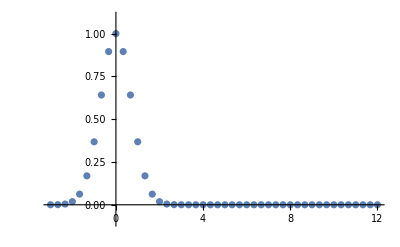

```mathematica
ListPlot[Table[{i,q0[i]},{i,xA,xB,dx}],PlotRange->{{xA,xB},{-0.1,1.1}}]
```

```mathematica
For[i=0,i≤P,i++,
Phi[i,0]=xA+i*dx;
Q[i]=q0[Phi[i,0]];
]
```

```mathematica
ListPlot[Table[{Phi[i,0],Q[i]},{i,0,P}],PlotRange->{{xA,xB},{-0.1,1.1}}]
```

-Graphics-

```mathematica
For[t=1,t<=M,t++,
For[i=0,i≤P,i++,
Phi[i,t]=Phi[i,t-1]+dt*v[Phi[i,t-1]];
]
]
```

```mathematica
Manipulate[Show[ListPlot[Table[{Phi[i,t],Q[i]},{i,0,P}],PlotRange->{{xA,xB},{-0.1,1.1}},Joined->True],
ListPlot[Table[{Phi[i,t],0.0},{i,0,P,5}],PlotRange->{{xA,xB},{-0.1,1.1}},
PlotStyle->Directive[Red,PointSize[Large]]]],{t,0,M,1}]
```

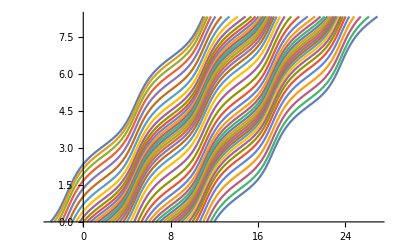

```mathematica
ListLinePlot[Table[{Phi[i,n],n*dt},{i,0,P},{n,0,M}]]
```

```mathematica
ListPlot3D[Flatten[Table[{Phi[i,t],t*dt,Q[i]},{i,0,P},{t,0,M}],1],PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
For[i=0,i≤P,i++,
l[i,0]=xA+i*dx;
r[i,0]=l[i,0]+dx;
ψ[i,0]=l[i,0]+(r[i,0]-l[i,0])/2;
ρ[i,0]=(q0[ψ[i,0]]);
hm[i]=ρ[i,0]+dx;
]
```

```mathematica
r[20,0]
```

4.

```mathematica
For[t=1,t<=M,t++,
For[i=0,i≤P,i++,
l[i,t]=l[i,t-1]+dt*v[l[i,t-1]];
r[i,t]=r[i,t-1]+dt*v[r[i,t-1]];
ψ[i,t]=l[i,t]+((r[i,t]-l[i,t])/2);
ρ[i,t]=hm[i]/(r[i,t]-l[i,t]);
]
]
```

```mathematica
Table[{l[i,5],r[i,5],ψ[i,5]},{i,10}]
```

{{-1.63774,-1.41596,-1.52685},{-1.41596,-1.13975,-1.27785},{-1.13975,-0.785376,-0.962562},{-0.785376,-0.328321,-0.556848},{-0.328321,0.241999,-0.043161},{0.241999,0.897372,0.569686},{0.897372,1.56175,1.22956},{1.56175,2.15048,1.85612},{2.15048,2.62325,2.38687},{2.62325,2.98797,2.80561}}

```mathematica
ρ[40,10]*(r[40,10]-l[40,10])
```

0.333333

```mathematica
Manipulate[Show[ListPlot[Table[{ψ[i,t],ρ[i,t]},{i,0,P}],PlotRange->{{xA,xB},{-0.1,1.1}},Joined->True],
ListPlot[Table[{ψ[i,t],0.0},{i,0,P,5}],PlotRange->{{xA,xB},{-0.1,1.1}},
PlotStyle->Directive[Red,PointSize[Large]]]],{t,0,M,1}]
```

```mathematica
Table[Sum[ρ[i,t]*(r[i,t]-l[i,t]),{i,0,P}],{t,1,10}]
```

{20.6506,20.6506,20.6506,20.6506,20.6506,20.6506,20.6506,20.6506,20.6506,20.6506}